{{1,2},{2,2509},{4,2486},{6,2494},{8,2510}}

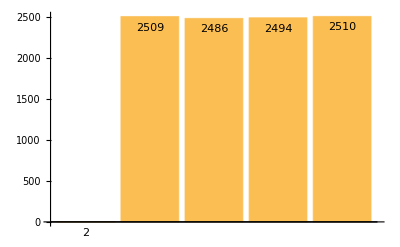

```mathematica
Clear[f];f[n_]:=Last[DeleteCases[IntegerDigits[n!],0]];
data=Sort[Tally[Table[f[i],{i,0,10000}]]]
BarChart[Last/@data,ChartLabels->Placed[Last/@data,Top],PlotRange->Automatic]
```

The chart above is the distribution of the last one of integer-digits of n! for n through 0 to 10000.
 It shows that totally digit 1 appears twice, and more interesting: 
 It looks as if the four main possibilities, 2, 4, 6, 8, are pretty evenly distributed.